# MAD-X TFS file reader

## Definitions

```mathematica
madFile[file_]:=Module[
{d,h,dPos,cols},
d=Import[file,"Table"];
h=Cases[d,{"@",___}|{"*",___}|{"$",___}];
d=Cases[d,Except[{"@",___}|{"*",___}|{"$",___}]];
cols=Rest@First@Cases[h,{"*",___}];
d=Thread[Rule@@{cols,Transpose@d}];
{h,d} (*extracts headings and data from a mad file*)
];
madFileToDataset::usage="Takes a mad optics file and returns {header, data}, where data is a Dataset with the columns specified as in the mad file.";
madFileToDataset[file_]:=Module[
{header,data,assocs,keys},
{header,data}=madFile[file];
keys=Keys[data];
assocs=Association[Thread[Rule[keys,#]]]&/@Transpose[keys/.data];
{header,Dataset[assocs]}
];

getTwissAtElement::usage="Takes a string and a data set and returns the list {\"BETX\",\"ALFX\",\"MUX\",\"BETY\",\"ALFY\",\"MUY\"} for the specified element.";
getTwissAtElement[element_String,opticsSet_Dataset]:=Module[
{entry,twiss},
entry=opticsSet[Select[StringMatchQ[element,#NAME]&]];
entry=First[Normal[entry]];
twiss=entry[[Key[#]]]&/@{"BETX","ALFX","MUX","BETY","ALFY","MUY"};
twiss
];
```

## Twiss Parameters Example

```mathematica
files={
FileNameJoin[{NotebookDirectory[],"optics-test-1"}],
FileNameJoin[{NotebookDirectory[],"optics-test-2"}]
};

{header,dataSet}=madFileToDataset[files[[1]]];
dataSet (*Comment/uncomment to hide/view the data set.*)
getTwissAtElement["QTV_C11",dataSet]

(*Applying to a list of files.*)

{#,getTwissAtElement["QTV_C11",Last@madFileToDataset[#]]}&/@files;
```

Dataset[<>]

{14.5012,0.573589,0.177203,15.5281,0.505342,0.142294}

```mathematica
TwissPos1=getTwissAtElement["Q25",dataSet] (*first location*)
TwissPos2=getTwissAtElement["MARK",dataSet] (*second location*)
```

{6.2227,-0.630381,2.83076,17.0843,1.66486,3.01741}

{68.9826,1.07345,3.39659,7.05838,-0.183575,3.40026}

## Define R Transform Matrix (RTM)

```mathematica
rTransformMatrix[{βx1_,αx1_,μx1_,βy1_,αy1_,μy1_},{βx2_,αx2_,μx2_,βy2_,αy2_,μy2_}]:={{√(βx2/βx1)(Cos[μx2-μx1]+αx1*Sin[μx2-μx1]),√(βx2*βx1)Sin[μx2-μx1],0,0},
{(-(1+αx2*αx1))/(√(βx2*βx1))Sin[μx2-μx1]+(αx1-αx2)/(√(βx2*βx1))Cos[μx2-μx1],√(βx1/βx2)(Cos[μx2-μx1]-αx2*Sin[μx2-μx1]),0,0},
{0,0,√(βy2/βy1)(Cos[μy2-μy1]+αy1*Sin[μy2-μy1]),√(βy2*βy1)Sin[μy2-μy1]},
{0,0,(-(1+αy2*αy1))/(√(βy2*βy1))Sin[μy2-μy1]+(αy1-αy2)/(√(βy2*βy1))Cos[μy2-μy1],√(βy1/βy2)(Cos[μy2-μy1]-αy2*Sin[μy2-μy1])}}
```

Test R Matrix

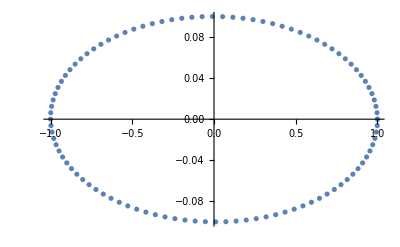
{-Graphics-,-Graphics-}

```mathematica
Module[
{test,tracked},
test=rTransformMatrix[{10,0.01,0,10,0.01,0},{10,0.01,2π*0.23,10,0.01,2π*0.23}];
tracked=NestList[test.#&,{1,0,1,0},100];
{ListPlot[tracked[[;;,{1,2}]]],ListPlot[tracked[[;;,{3,4}]]]}
]
```

## Calculate R - Single Optics, Multiple WS (SOMWS)

Definitions

```mathematica
somwsFile=FileNameJoin[{"/Users/4tc/Dropbox/suli 2018 project/optics_0001","BeamInfo.mu.txt"}]; (*contains BET, ALF, MU data*)
{somwsDataHeader,somwsDataSet}=madFileToDataset[somwsFile];
somwsStartPos="SURV$START"; (****INPUT NEEDED****) (*reconstruction point, s0, string*)
somwsEndPos =List["WS02","WS20","WS21","WS23","WS24"]; (*wire scanner location LIST of strings*)
```

Calculation

```mathematica
somwsStartTwiss=getTwissAtElement[somwsStartPos,somwsDataSet]; (*get twiss at start*)
somwsEndTwiss1=getTwissAtElement[somwsEndPos[[1]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss2=getTwissAtElement[somwsEndPos[[2]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss3=getTwissAtElement[somwsEndPos[[3]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss4=getTwissAtElement[somwsEndPos[[4]],somwsDataSet]; (*get twiss at one endpoint*)
somwsEndTwiss5=getTwissAtElement[somwsEndPos[[5]],somwsDataSet]; (*get twiss at one endpoint*)

somwsR1=rTransformMatrix[somwsStartTwiss,somwsEndTwiss1];(*calculate RTM*)
somwsR2=rTransformMatrix[somwsStartTwiss,somwsEndTwiss2];(*calculate RTM*)
somwsR3=rTransformMatrix[somwsStartTwiss,somwsEndTwiss3];(*calculate RTM*)
somwsR4=rTransformMatrix[somwsStartTwiss,somwsEndTwiss4]; (*calculate RTM*)
somwsR5=rTransformMatrix[somwsStartTwiss,somwsEndTwiss5]; (*calculate RTM*)
somwsRs={somwsR1, somwsR2,somwsR3, somwsR4,somwsR5};
MatrixForm/@somwsRs
```

{(0.467772 | 0.610493 | 0 | 0
-0.590904 | 1.3666 | 0 | 0
0 | 0 | 1.26163 | 1.01332
0 | 0 | 0.407997 | 1.12032),(-2.42392 | 7.00351 | 0 | 0
0.772639 | -2.64497 | 0 | 0
0 | 0 | 3.44741 | 10.7875
0 | 0 | 0.13446 | 0.71082),(-6.32198 | 17.6979 | 0 | 0
-1.19441 | 3.18547 | 0 | 0
0 | 0 | 2.10333 | 6.79322
0 | 0 | -0.38021 | -0.752545),(-9.64053 | 26.6202 | 0 | 0
-0.78621 | 2.06721 | 0 | 0
0 | 0 | 3.6449 | 12.4135
0 | 0 | -0.708231 | -2.13769),(-4.08784 | 11.2099 | 0 | 0
1.53112 | -4.44335 | 0 | 0
0 | 0 | 4.12329 | 14.351
0 | 0 | 0.119944 | 0.659989)}

## Calculate R - Multiple Optics, Single WS (MOSWS)

Definitions

```mathematica
moswsFiles={
FileNameJoin[{"/Users/4tc/Dropbox/suli 2018 project/optics_*","BeamInfo.mu.txt"}]
};
moswsFiles=FileNames[moswsFiles];
moswsStartPos="SURV$START"; (****INPUT NEEDED****) (*reconstruction point, s0, string*)
moswsEndPos ="WS20"; (****INPUT NEEDED****) (*ONE wire scanner location, string*)
```

Calculation

```mathematica
(*apply to full list of files*)
moswsStartTwiss=getTwissAtElement[moswsStartPos,Last@madFileToDataset[#]]&/@moswsFiles;(*get twiss at start, list of 6-item lists*)
moswsEndTwiss=getTwissAtElement[moswsEndPos,Last@madFileToDataset[#]]&/@moswsFiles; (*get twiss at end, list of 6-item lists*)

moswsRs=Table[
rTransformMatrix[moswsStartTwiss[[j]],moswsEndTwiss[[j]]],(*calculate RTM*)
{j,1,Length@moswsEndTwiss}
];
ClearAll[j];
MatrixForm/@moswsRs
```

{(-2.42392 | 7.00351 | 0 | 0
0.772639 | -2.64497 | 0 | 0
0 | 0 | 3.44741 | 10.7875
0 | 0 | 0.13446 | 0.71082),(-2.64268 | 7.53901 | 0 | 0
0.0713181 | -0.581859 | 0 | 0
0 | 0 | 3.68958 | 11.1979
0 | 0 | 0.326368 | 1.26156),(-2.87104 | 8.08243 | 0 | 0
0.458069 | -1.63784 | 0 | 0
0 | 0 | 4.85039 | 14.6424
0 | 0 | 0.492925 | 1.69422),(-2.75888 | 7.73607 | 0 | 0
0.312481 | -1.23868 | 0 | 0
0 | 0 | 7.67929 | 24.0672
0 | 0 | 0.781149 | 2.57837),(-2.6429 | 7.61587 | 0 | 0
-0.00811574 | -0.354986 | 0 | 0
0 | 0 | 6.02064 | 18.8251
0 | 0 | 0.678175 | 2.28658),(-2.65976 | 7.67004 | 0 | 0
-0.0215595 | -0.313802 | 0 | 0
0 | 0 | 4.4421 | 13.9724
0 | 0 | 0.477527 | 1.72715),(-3.21831 | 8.89236 | 0 | 0
1.40573 | -4.19484 | 0 | 0
0 | 0 | 3.59734 | 10.5874
0 | 0 | 0.34046 | 1.27999),(-3.06719 | 8.655 | 0 | 0
0.781283 | -2.53066 | 0 | 0
0 | 0 | 3.51568 | 10.642
0 | 0 | 0.225683 | 0.967585),(-3.38707 | 9.59138 | 0 | 0
1.33037 | -4.06254 | 0 | 0
0 | 0 | 3.84857 | 11.4892
0 | 0 | 0.420004 | 1.51368),(-3.34752 | 9.46761 | 0 | 0
1.27846 | -3.91454 | 0 | 0
0 | 0 | 6.02745 | 17.8555
0 | 0 | 0.744879 | 2.37251)}

## Calculate R - Combination SOMWS and MOSWS (COMBO)

Definitions

```mathematica
comboFiles={                           (* specify folder(s) *)
FileNameJoin[{"/Users/4tc/Dropbox/suli 2018 project/y_optics_*","BeamInfo.mu.txt"}]
};
comboFiles=FileNames[comboFiles];
comboList=madFileToDataset[#]&/@comboFiles;
comboList=Transpose[comboList];
comboDataHeaders=comboList[[1]];
comboDataSets=comboList[[2]];
comboStartPos="SURV$START"; (****INPUT NEEDED****) (*reconstruction point, s0, string*)
comboEndPos ={"WS02","WS20","WS21","WS23","WS24"}; (****INPUT NEEDED****) (* which wire scanners to use *)(*wire scanner location LIST of strings*)
```

Calculation

```mathematica
(*apply to full list of files*)
comboStartTwiss=getTwissAtElement[comboStartPos,#]&/@comboDataSets; (*get twiss at start, N-item list of 6-item lists*)
comboEndTwiss={getTwissAtElement[comboEndPos[[1]],#]&/@comboDataSets,
getTwissAtElement[comboEndPos[[2]],#]&/@comboDataSets,
getTwissAtElement[comboEndPos[[3]],#]&/@comboDataSets,
getTwissAtElement[comboEndPos[[4]],#]&/@comboDataSets,
getTwissAtElement[comboEndPos[[5]],#]&/@comboDataSets};(*get twiss at end. 5-item list of N-item lists of 6-item lists*) 

comboEndTwiss=Transpose[comboEndTwiss,{2,1,3}]; (*sort by optics, then position, then twiss*)
comboRs=Table[
rTransformMatrix[RotateRight[comboStartTwiss[[j]],3],RotateRight[comboEndTwiss[[j,k]] ,3]],(*calculate RTM*)
{k,1,Length@comboEndPos}, (* for all wire scanners *)
{j,1,Length@comboEndTwiss} (* for all optics *)
];
ClearAll[j,k];

comboRs=Flatten[comboRs,1]; 
MatrixForm/@comboRs
```

{(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(1.26163 | 1.01332 | 0 | 0
0.407997 | 1.12032 | 0 | 0
0 | 0 | 0.467772 | 0.610493
0 | 0 | -0.590904 | 1.3666),(3.562 | 11.0708 | 0 | 0
0.265534 | 1.10603 | 0 | 0
0 | 0 | -2.84905 | 8.18638
0 | 0 | 0.131657 | -0.729294),(3.67145 | 11.4219 | 0 | 0
0.270279 | 1.11321 | 0 | 0
0 | 0 | -2.85502 | 8.20753
0 | 0 | 0.138623 | -0.748769),(3.67707 | 11.4526 | 0 | 0
0.308314 | 1.23223 | 0 | 0
0 | 0 | -2.64854 | 7.5977
0 | 0 | 0.0525825 | -0.528407),(3.86891 | 12.064 | 0 | 0
0.302795 | 1.20265 | 0 | 0
0 | 0 | -2.71047 | 7.78791
0 | 0 | 0.097837 | -0.650051),(4.13918 | 12.9217 | 0 | 0
0.295164 | 1.16304 | 0 | 0
0 | 0 | -2.71043 | 7.78219
0 | 0 | 0.0526509 | -0.520116),(3.81732 | 11.9307 | 0 | 0
0.354305 | 1.36931 | 0 | 0
0 | 0 | -2.8666 | 8.29004
0 | 0 | 0.312488 | -1.25254),(3.91092 | 12.2374 | 0 | 0
0.377888 | 1.43812 | 0 | 0
0 | 0 | -2.79429 | 8.08292
0 | 0 | 0.321586 | -1.28811),(4.05552 | 12.7046 | 0 | 0
0.375777 | 1.42376 | 0 | 0
0 | 0 | -3.0102 | 8.72712
0 | 0 | 0.356304 | -1.3652),(5.16576 | 16.2014 | 0 | 0
0.261847 | 1.01482 | 0 | 0
0 | 0 | -2.8373 | 8.18086
0 | 0 | 0.0939453 | -0.623324),(5.55427 | 17.4402 | 0 | 0
0.254166 | 0.978116 | 0 | 0
0 | 0 | -2.66861 | 7.68076
0 | 0 | 0.00470078 | -0.388257),(5.67764 | 17.8484 | 0 | 0
0.272082 | 1.03145 | 0 | 0
0 | 0 | -2.6046 | 7.5088
0 | 0 | 0.0397233 | -0.498454),(5.72479 | 18.0176 | 0 | 0
0.274632 | 1.03903 | 0 | 0
0 | 0 | -2.89092 | 8.37416
0 | 0 | 0.130955 | -0.72525),(5.47621 | 17.2554 | 0 | 0
0.387621 | 1.40399 | 0 | 0
0 | 0 | -2.66335 | 7.72446
0 | 0 | 0.263263 | -1.139),(5.88929 | 18.5788 | 0 | 0
0.340563 | 1.24417 | 0 | 0
0 | 0 | -2.8743 | 8.35209
0 | 0 | 0.191588 | -0.904625),(6.13714 | 19.3835 | 0 | 0
0.364242 | 1.31336 | 0 | 0
0 | 0 | -2.79265 | 8.12223
0 | 0 | 0.208171 | -0.963535),(6.38978 | 20.2051 | 0 | 0
0.433138 | 1.52613 | 0 | 0
0 | 0 | -2.58377 | 7.51957
0 | 0 | 0.31838 | -1.31361),(6.68185 | 21.1536 | 0 | 0
0.511968 | 1.77046 | 0 | 0
0 | 0 | -2.5052 | 7.30048
0 | 0 | 0.460156 | -1.74013),(6.99481 | 22.1705 | 0 | 0
0.616772 | 2.09786 | 0 | 0
0 | 0 | -2.53613 | 7.40288
0 | 0 | 0.660916 | -2.3235),(7.39769 | 23.4752 | 0 | 0
0.718553 | 2.41537 | 0 | 0
0 | 0 | -2.66225 | 7.78369
0 | 0 | 0.868954 | -2.91621),(7.33396 | 23.3006 | 0 | 0
0.735032 | 2.47161 | 0 | 0
0 | 0 | -3.09844 | 9.07233
0 | 0 | 0.807659 | -2.6876),(7.53906 | 23.9729 | 0 | 0
0.755039 | 2.53354 | 0 | 0
0 | 0 | -3.27807 | 9.60531
0 | 0 | 0.812899 | -2.68699),(2.45937 | 7.84063 | 0 | 0
-0.366528 | -0.761908 | 0 | 0
0 | 0 | -7.38618 | 20.8617
0 | 0 | -1.15468 | 3.12592),(2.45404 | 7.82452 | 0 | 0
-0.401488 | -0.872621 | 0 | 0
0 | 0 | -7.34939 | 20.7665
0 | 0 | -1.14831 | 3.10861),(2.58139 | 8.22807 | 0 | 0
-0.389984 | -0.855671 | 0 | 0
0 | 0 | -7.78917 | 21.9535
0 | 0 | -1.26824 | 3.4461),(2.5344 | 8.08067 | 0 | 0
-0.453143 | -1.05023 | 0 | 0
0 | 0 | -7.56008 | 21.3389
0 | 0 | -1.21769 | 3.30474),(2.47775 | 7.90036 | 0 | 0
-0.538967 | -1.31492 | 0 | 0
0 | 0 | -7.74899 | 21.8688
0 | 0 | -1.24931 | 3.39668),(2.72489 | 8.69532 | 0 | 0
-0.416374 | -0.961692 | 0 | 0
0 | 0 | -6.61364 | 18.7507
0 | 0 | -1.0445 | 2.81009),(2.79889 | 8.93147 | 0 | 0
-0.432725 | -1.02357 | 0 | 0
0 | 0 | -6.62185 | 18.7646
0 | 0 | -1.0663 | 2.87061),(2.77893 | 8.87244 | 0 | 0
-0.47748 | -1.16462 | 0 | 0
0 | 0 | -6.37093 | 18.114
0 | 0 | -0.979939 | 2.62923),(2.32151 | 7.41135 | 0 | 0
-0.851521 | -2.2877 | 0 | 0
0 | 0 | -7.47684 | 21.1952
0 | 0 | -1.1841 | 3.2229),(2.2995 | 7.34103 | 0 | 0
-0.9607 | -2.6321 | 0 | 0
0 | 0 | -7.91092 | 22.383
0 | 0 | -1.29541 | 3.53881),(2.37177 | 7.57358 | 0 | 0
-0.983341 | -2.7184 | 0 | 0
0 | 0 | -7.77639 | 22.0171
0 | 0 | -1.29132 | 3.5275),(2.38515 | 7.62333 | 0 | 0
-0.995945 | -2.76394 | 0 | 0
0 | 0 | -7.23316 | 20.5936
0 | 0 | -1.14346 | 3.11731),(2.80794 | 8.96888 | 0 | 0
-0.855955 | -2.37788 | 0 | 0
0 | 0 | -6.86634 | 19.5013
0 | 0 | -1.14813 | 3.11521),(2.64692 | 8.4627 | 0 | 0
-0.994885 | -2.80304 | 0 | 0
0 | 0 | -6.94806 | 19.8222
0 | 0 | -1.11036 | 3.02383),(2.75386 | 8.80536 | 0 | 0
-1.03977 | -2.96151 | 0 | 0
0 | 0 | -6.9056 | 19.7005
0 | 0 | -1.12773 | 3.07242),(3.04155 | 9.7206 | 0 | 0
-1.04871 | -3.02282 | 0 | 0
0 | 0 | -6.74505 | 19.1889
0 | 0 | -1.16916 | 3.17788),(3.37767 | 10.7912 | 0 | 0
-1.05594 | -3.07752 | 0 | 0
0 | 0 | -6.53803 | 18.566
0 | 0 | -1.18522 | 3.2127),(3.82506 | 12.2172 | 0 | 0
-1.04448 | -3.07464 | 0 | 0
0 | 0 | -6.20788 | 17.5942
0 | 0 | -1.17864 | 3.17938),(4.27486 | 13.6537 | 0 | 0
-1.05418 | -3.13308 | 0 | 0
0 | 0 | -5.86355 | 16.5889
0 | 0 | -1.16772 | 3.13313),(4.33701 | 13.868 | 0 | 0
-1.027 | -3.05335 | 0 | 0
0 | 0 | -5.14064 | 14.6327
0 | 0 | -0.914694 | 2.40912),(4.44019 | 14.2055 | 0 | 0
-1.05765 | -3.15853 | 0 | 0
0 | 0 | -4.93711 | 14.084
0 | 0 | -0.834046 | 2.17672),(3.36446 | 11.2622 | 0 | 0
-0.712324 | -2.08721 | 0 | 0
0 | 0 | -7.16396 | 19.9098
0 | 0 | -0.423788 | 1.03819),(3.28419 | 11.0233 | 0 | 0
-0.689128 | -2.00854 | 0 | 0
0 | 0 | -7.15555 | 19.8924
0 | 0 | -0.427425 | 1.04849),(3.19721 | 10.7033 | 0 | 0
-0.706019 | -2.05077 | 0 | 0
0 | 0 | -7.74298 | 21.5231
0 | 0 | -0.449155 | 1.11936),(3.09802 | 10.4309 | 0 | 0
-0.659417 | -1.89744 | 0 | 0
0 | 0 | -7.55196 | 21.0038
0 | 0 | -0.45023 | 1.11978),(3.03836 | 10.3093 | 0 | 0
-0.601021 | -1.71017 | 0 | 0
0 | 0 | -7.5828 | 21.0966
0 | 0 | -0.437288 | 1.08473),(3.01349 | 10.1019 | 0 | 0
-0.703861 | -2.02767 | 0 | 0
0 | 0 | -7.35024 | 20.468
0 | 0 | -0.526042 | 1.3288),(2.92221 | 9.79969 | 0 | 0
-0.700247 | -2.00608 | 0 | 0
0 | 0 | -7.55366 | 21.0375
0 | 0 | -0.545046 | 1.38561),(2.83208 | 9.54095 | 0 | 0
-0.664589 | -1.88582 | 0 | 0
0 | 0 | -7.15609 | 19.9518
0 | 0 | -0.540151 | 1.36625),(3.41304 | 11.897 | 0 | 0
-0.476313 | -1.36731 | 0 | 0
0 | 0 | -7.28018 | 20.3182
0 | 0 | -0.439437 | 1.08906),(3.68315 | 12.9286 | 0 | 0
-0.464248 | -1.3581 | 0 | 0
0 | 0 | -7.79597 | 21.7625
0 | 0 | -0.455276 | 1.14263),(3.64228 | 12.8124 | 0 | 0
-0.449225 | -1.30568 | 0 | 0
0 | 0 | -7.96799 | 22.2593
0 | 0 | -0.488368 | 1.2388),(3.64058 | 12.8327 | 0 | 0
-0.44563 | -1.29613 | 0 | 0
0 | 0 | -7.21535 | 20.2084
0 | 0 | -0.467725 | 1.17139),(2.83994 | 9.91684 | 0 | 0
-0.415671 | -1.09937 | 0 | 0
0 | 0 | -7.92844 | 22.1694
0 | 0 | -0.570239 | 1.46837),(3.32909 | 11.7549 | 0 | 0
-0.401686 | -1.11796 | 0 | 0
0 | 0 | -7.33993 | 20.5894
0 | 0 | -0.513214 | 1.30339),(3.34551 | 11.8524 | 0 | 0
-0.3809 | -1.05054 | 0 | 0
0 | 0 | -7.58616 | 21.2915
0 | 0 | -0.542493 | 1.39075),(3.10398 | 11.0052 | 0 | 0
-0.338159 | -0.876775 | 0 | 0
0 | 0 | -8.34241 | 23.3805
0 | 0 | -0.631922 | 1.65116),(2.83812 | 10.0663 | 0 | 0
-0.295036 | -0.694093 | 0 | 0
0 | 0 | -8.92347 | 24.9788
0 | 0 | -0.712368 | 1.88201),(2.44992 | 8.67293 | 0 | 0
-0.257557 | -0.503598 | 0 | 0
0 | 0 | -9.50652 | 26.564
0 | 0 | -0.805203 | 2.14478),(2.15242 | 7.61029 | 0 | 0
-0.231728 | -0.354727 | 0 | 0
0 | 0 | -10.0933 | 28.1547
0 | 0 | -0.901404 | 2.41534),(2.01885 | 7.12657 | 0 | 0
-0.255122 | -0.405253 | 0 | 0
0 | 0 | -8.95178 | 24.9928
0 | 0 | -0.850014 | 2.26148),(2.03035 | 7.18951 | 0 | 0
-0.230941 | -0.325241 | 0 | 0
0 | 0 | -8.70158 | 24.2979
0 | 0 | -0.852295 | 2.26499),(3.76809 | 12.9552 | 0 | 0
0.11407 | 0.657575 | 0 | 0
0 | 0 | -2.8163 | 7.71777
0 | 0 | 1.14582 | -3.49507),(3.80915 | 13.1355 | 0 | 0
0.132042 | 0.717862 | 0 | 0
0 | 0 | -2.83136 | 7.76187
0 | 0 | 1.14011 | -3.47867),(3.62987 | 12.5159 | 0 | 0
0.117119 | 0.67932 | 0 | 0
0 | 0 | -2.82162 | 7.74308
0 | 0 | 1.28332 | -3.8761),(3.7818 | 13.1069 | 0 | 0
0.154925 | 0.801361 | 0 | 0
0 | 0 | -2.85381 | 7.83427
0 | 0 | 1.23014 | -3.72739),(4.03985 | 14.0845 | 0 | 0
0.2051 | 0.962591 | 0 | 0
0 | 0 | -2.79618 | 7.6768
0 | 0 | 1.24275 | -3.76956),(3.47825 | 12.0526 | 0 | 0
0.1206 | 0.705396 | 0 | 0
0 | 0 | -3.19002 | 8.77824
0 | 0 | 1.12942 | -3.4214),(3.42994 | 11.9109 | 0 | 0
0.128144 | 0.736546 | 0 | 0
0 | 0 | -3.2365 | 8.91217
0 | 0 | 1.16959 | -3.52962),(3.53687 | 12.3349 | 0 | 0
0.15662 | 0.828949 | 0 | 0
0 | 0 | -3.27523 | 9.02382
0 | 0 | 1.06508 | -3.23981),(5.2398 | 18.5888 | 0 | 0
0.360502 | 1.46977 | 0 | 0
0 | 0 | -2.84547 | 7.834
0 | 0 | 1.144 | -3.50105),(5.71846 | 20.3715 | 0 | 0
0.40996 | 1.63532 | 0 | 0
0 | 0 | -2.82534 | 7.78734
0 | 0 | 1.26925 | -3.8523),(5.75152 | 20.534 | 0 | 0
0.421975 | 1.6804 | 0 | 0
0 | 0 | -2.93227 | 8.09461
0 | 0 | 1.29216 | -3.90809),(5.77057 | 20.6427 | 0 | 0
0.425401 | 1.69505 | 0 | 0
0 | 0 | -2.95593 | 8.17062
0 | 0 | 1.09357 | -3.36109),(4.88238 | 17.4432 | 0 | 0
0.379547 | 1.56082 | 0 | 0
0 | 0 | -3.2728 | 9.05474
0 | 0 | 1.23067 | -3.71039),(5.5864 | 20.0566 | 0 | 0
0.436507 | 1.74618 | 0 | 0
0 | 0 | -3.11023 | 8.6189
0 | 0 | 1.09616 | -3.35914),(5.74163 | 20.6704 | 0 | 0
0.46326 | 1.84195 | 0 | 0
0 | 0 | -3.18881 | 8.84808
0 | 0 | 1.14165 | -3.48135),(5.67596 | 20.4797 | 0 | 0
0.487131 | 1.93382 | 0 | 0
0 | 0 | -3.47263 | 9.64117
0 | 0 | 1.28459 | -3.85441),(5.60927 | 20.2853 | 0 | 0
0.514908 | 2.04038 | 0 | 0
0 | 0 | -3.76646 | 10.4585
0 | 0 | 1.37545 | -4.08477),(5.43904 | 19.7108 | 0 | 0
0.543039 | 2.1518 | 0 | 0
0 | 0 | -4.13439 | 11.4737
0 | 0 | 1.45106 | -4.26881),(5.39408 | 19.596 | 0 | 0
0.582145 | 2.30025 | 0 | 0
0 | 0 | -4.53028 | 12.5629
0 | 0 | 1.51803 | -4.43035),(5.21223 | 18.9633 | 0 | 0
0.569873 | 2.26519 | 0 | 0
0 | 0 | -4.3847 | 12.1579
0 | 0 | 1.28806 | -3.79961),(5.34284 | 19.4776 | 0 | 0
0.591565 | 2.34374 | 0 | 0
0 | 0 | -4.41699 | 12.2474
0 | 0 | 1.22643 | -3.62705)}

## Build Measurement Matrix (SOMWS or MOSWS)

```mathematica
(****INPUT NEEDED****)(*what measurements?*)

(*moswsRs={};*) (*<-- uncomment to test with empty set*)
(*listOfRs=somwsRs;*)
(*listOfRs=moswsRs;*)
(*listOfRs=Join[somwsRs, moswsRs];*)
listOfRs=comboRs;

ClearAll[r,σ,orderedSigmaElements,generalMeasurementMatrix]
{orderedSigmaElements,generalMeasurementMatrix}=Module[
{
rmat=Table[r[i,j],{i,1,4},{j,1,4}],
σmat=Table[σ[Min[i,j],Max[i,j]],{i,1,4},{j,1,4}],
unknowns,
trans,coefficients,dummy=Array[0&,{10,3}]
},
trans=(rmat.σmat.Transpose[rmat])[[Sequence@@#]]&/@{{1,1},{3,3},{1,3}};(*Take elements xx,yy,xy from σ'*)
unknowns=DeleteDuplicates[Flatten[σmat]];(*This is how our unknown column vector will be ordered, so we'll save it at the end.*)
coefficients=Table[{#,Coefficient[trans[[i]],#,1]}&/@unknowns,{i,1,Length@trans}];(*We extract the coeffecients in terms of r for each element of σ, each unknown.*)
{unknowns,Table[coefficients[[i,j,2]],{i,1,Length@trans},{j,1,Length@unknowns}]}
];

(*We can set the coupling elements to 0.*)
uncoupledMeasurementMatrix=generalMeasurementMatrix/.{r[1,3]->0,r[1,4]->0,r[2,3]->0,r[2,4]->0,r[3,1]->0,r[3,2]->0,r[4,2]->0,r[4,1]->0};

(*
Using the notation r[scanIndex][plane index,σ index] we can give the full uncoupled measurement matrix in general form. From here solving the problem is just a matter of taking the least squares where the answer will be returned as {...10 numbers...}. 
*)

fullUncoupledMeasurementMatrix=Join@@Table[
uncoupledMeasurementMatrix/.Flatten[Table[r[i,j]->r[scanIndex][i,j],{i,1,4},{j,1,4}]],
{scanIndex,1,Length@listOfRs}
];
MatrixForm@fullUncoupledMeasurementMatrix;
For[ (* define all r terms in meas matrix *)
i=1,i≤Length@listOfRs,i++,
rules={r[i][1,1]->listOfRs[[i]][[1,1]],r[i][1,2]->listOfRs[[i]][[1,2]],
r[i][2,1]->listOfRs[[i]][[2,1]],r[i][2,2]->listOfRs[[i]][[2,2]],
r[i][3,3]->listOfRs[[i]][[3,3]],r[i][3,4]->listOfRs[[i]][[3,4]],
r[i][4,3]->listOfRs[[i]][[4,3]],r[i][4,4]->listOfRs[[i]][[4,4]]};
fullUncoupledMeasurementMatrix=fullUncoupledMeasurementMatrix/.rules;
];
ClearAll[i];

MatrixForm@fullUncoupledMeasurementMatrix;
```

## Sigma Matrix Reconstruction

Wire Scanner Measurements

```mathematica
dataWSX=FileNames[{"~/Dropbox/suli 2018 project/y_optics*/ws_*_x.dat"}]; (* specify folder(s) *)
dataWSY=FileNames[{"~/Dropbox/suli 2018 project/y_optics*/ws_*_y.dat"}];
dataWSD=FileNames[{"~/Dropbox/suli 2018 project/y_optics*/ws_*_d.dat"}];

variances[num_Integer,xData_List,yData_List,dData_List]:=Module[   (*calculates x, y, and xy variances from input data lists and outputs them in a list of three*) 
{numb,tabX,tabY,tabD,sigx,sigy,sigd,x,wx,y,wy,d,wd,vars},
numb=num;
tabX=Import[xData[[numb]],"Table"];
{x,wx}=Drop[Transpose[tabX],1];
sigx=Variance @ WeightedData[x,wx](* <xx> *);
tabY=Import[yData[[numb]],"Table"];
{y,wy}=Drop[Transpose[tabY],1];
sigy=Variance @ WeightedData[y,wy](* <yy> *);
tabD=Import[dData[[numb]],"Table"];
{d,wd}=Drop[Transpose[tabD],1];
sigd=Variance [ WeightedData[d,wd]] -0.5*(sigx+sigy)(* <xy> *);
vars={sigy,sigx,sigd}
]

(*ws00Vars=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[1,Length@dataWSY,6];*)      (*at WS00 only*)
ws02Vars=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[2,Length@dataWSY,6];      (*at WS02 only*)
ws20Vars=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[3,Length@dataWSY,6];      (*at WS20 only*)
ws21Vars=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[4,Length@dataWSY,6];      (*at WS21 only*)
ws23Vars=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[5,Length@dataWSY,6];      (*at WS23 only*)
ws24Vars=variances[#, dataWSX,dataWSY,dataWSD]&/@Range[6,Length@dataWSY,6];      (*at WS24 only*)
(*measurements00=Flatten@ws00Vars;*)
measurements02=Flatten@ws02Vars;
measurements20=Flatten@ws20Vars;
measurements21=Flatten@ws21Vars;
measurements23=Flatten@ws23Vars;
measurements24=Flatten@ws24Vars;
measurements=(10^-6)*Flatten[{measurements02,measurements20,measurements21,measurements23,measurements24}];
Length@measurements
```

315

Visualization of Least Squares Formula

```mathematica
fullEq=Row[
{
measurements//MatrixForm
(*=MatrixForm[List/@Join@@Table[{"σ_xx"[i],"σ_yy"[i],"σ_xy"[i]},{i,1,Length@listOfRs}]] *)," = ",
(MatrixForm@fullUncoupledMeasurementMatrix).MatrixForm[List/@orderedSigmaElements]
}
]
```

(64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
64.4773
84.1272
-0.014489
411813.
271.37
27770.
411803.
271.4
19448.7
411789.
271.426
27773.1
411787.
271.448
27754.1
411745.
271.481
27773.3
411736.
271.507
27769.4
411722.
271.548
27769.2
411714.
271.56
27756.6
411671.
271.617
27770.6
411661.
271.65
27769.2
411659.
271.669
27754.1
411643.
271.699
27768.2
411635.
271.727
27750.4
411593.
271.748
25814.7
411584.
271.774
25813.2
363772.
309.198
-14113.9
345568.
367.138
-67343.2
380601.
729.332
-143286.
326415.
952.211
-138317.
225184.
1147.5
-98863.2
127475.
1529.56
-56895.2
114147.
1808.15
-51715.4
114147.
1808.18
-51715.4
114140.
1808.1
-51711.9
114134.
1808.13
-51709.5
114134.
1808.05
-51709.4
114133.
1807.06
-51708.4
114133.
1808.11
-51709.
114133.
1808.13
-51709.1
114128.
1808.15
-51706.
1.7237×10^6
193.291
100638.
1.7237×10^6
193.296
100637.
1.72369×10^6
193.302
100651.
1.72369×10^6
193.306
100644.
1.72366×10^6
193.313
100655.
1.72369×10^6
193.318
100640.
1.72369×10^6
193.324
100638.
1.72369×10^6
193.329
100541.
1.72369×10^6
193.337
100529.
1.72367×10^6
193.341
100537.
1.72366×10^6
193.346
100540.
1.72352×10^6
193.351
100609.
1.72355×10^6
193.359
100598.
1.72355×10^6
193.364
100597.
1.72354×10^6
193.37
66683.2
1.63105×10^6
213.002
93827.5
1.76355×10^6
237.394
80764.2
2.24158×10^6
172.612
85548.9
2.50841×10^6
181.892
100132.
2.39747×10^6
241.639
97293.2
1.53195×10^6
467.946
140968.
1.2247×10^6
626.689
127210.
1.22469×10^6
626.699
127211.
1.22469×10^6
626.701
127211.
1.2247×10^6
626.712
127217.
1.22469×10^6
626.72
127211.
1.2247×10^6
626.726
127208.
1.18117×10^6
626.736
148975.
1.22457×10^6
626.741
127265.
1.22457×10^6
626.75
127158.
68773.
84.3617
743.087
68781.3
84.3506
743.945
68788.
84.336
744.697
68796.
84.3151
746.529
68806.3
84.3009
745.15
68814.6
84.2836
-424.74
68824.7
84.2844
744.867
68835.5
84.2806
744.506
68843.6
84.2601
745.46
68853.8
84.2577
744.583
68862.1
84.2391
745.184
68872.4
84.2315
744.731
68878.9
84.2316
745.04
68887.1
84.2176
746.348
68897.3
84.1996
848.666
89501.2
75.6824
75.1814
163549.
62.5896
833.249
306435.
209.801
5305.42
614384.
373.495
-18999.3
950586.
369.85
-55451.4
693995.
193.572
-28593.5
481661.
133.67
-13117.1
498944.
133.677
-21758.8
498944.
133.626
-21762.8
498944.
133.687
-21762.9
498944.
133.681
-21763.
498950.
133.687
-21766.1
498950.
133.692
-21766.8
498950.
133.643
-21766.6
498948.
133.7
-21765.6
96009.
123.594
-43335.4
95716.4
123.577
-43190.6
95980.6
123.575
-43324.1
95966.7
123.568
-43318.7
95953.7
123.575
-43313.8
95668.2
123.546
-43171.5
95929.2
123.579
-43302.7
95914.7
123.581
-43297.7
95905.3
123.615
-43294.7
95891.5
123.637
-43289.4
95881.5
123.651
-43284.8
95867.9
123.673
-43278.7
95853.9
123.686
-43272.4
95844.
123.694
-43267.9
95828.8
123.738
-43261.1
71025.5
134.945
-32399.7
37772.8
162.132
-17031.4
24512.6
946.515
-11384.4
43.0907
1409.17
45.0162
5617.6
1580.35
-1688.91
9815.72
1567.9
-2900.19
5816.83
1621.83
-1447.69
5817.03
1621.87
-1447.79
5817.01
1621.91
-1447.82
5640.56
1621.18
-1359.21
5816.99
1621.98
-1447.81
5816.95
1622.01
-1447.78
5816.96
1622.05
-1447.66
5816.97
1622.09
-1447.69
5817.45
1622.12
-1447.94) = (0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
0.218811 | 0.571144 | 0 | 0 | 0.372702 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.59172 | 2.55687 | 1.02681
0 | 0 | 0.590157 | 0.474001 | 0 | 0.770219 | 0.618623 | 0 | 0 | 0
8.12299 | -46.6812 | 0 | 0 | 67.0667 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6787 | 78.8102 | 122.47
0 | 0 | -10.1483 | -31.5408 | 0 | 29.1602 | 90.6293 | 0 | 0 | 0
8.12258 | -46.6788 | 0 | 0 | 67.0633 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6793 | 78.8143 | 122.477
0 | 0 | -10.1483 | -31.5409 | 0 | 29.1602 | 90.6294 | 0 | 0 | 0
8.12217 | -46.6764 | 0 | 0 | 67.0598 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.68 | 78.8183 | 122.483
0 | 0 | -10.1483 | -31.5409 | 0 | 29.1602 | 90.6294 | 0 | 0 | 0
8.12176 | -46.674 | 0 | 0 | 67.0563 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6806 | 78.8224 | 122.49
0 | 0 | -10.1483 | -31.5409 | 0 | 29.1602 | 90.6295 | 0 | 0 | 0
8.12135 | -46.6716 | 0 | 0 | 67.0529 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6812 | 78.8265 | 122.496
0 | 0 | -10.1483 | -31.541 | 0 | 29.1601 | 90.6295 | 0 | 0 | 0
8.12094 | -46.6692 | 0 | 0 | 67.0494 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6819 | 78.8305 | 122.503
0 | 0 | -10.1483 | -31.541 | 0 | 29.1601 | 90.6296 | 0 | 0 | 0
8.12052 | -46.6668 | 0 | 0 | 67.0459 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6825 | 78.8346 | 122.509
0 | 0 | -10.1483 | -31.541 | 0 | 29.1601 | 90.6296 | 0 | 0 | 0
8.12011 | -46.6644 | 0 | 0 | 67.0425 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6832 | 78.8386 | 122.515
0 | 0 | -10.1483 | -31.5411 | 0 | 29.1601 | 90.6297 | 0 | 0 | 0
8.1197 | -46.662 | 0 | 0 | 67.039 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6838 | 78.8427 | 122.522
0 | 0 | -10.1483 | -31.5411 | 0 | 29.1601 | 90.6297 | 0 | 0 | 0
8.11928 | -46.6596 | 0 | 0 | 67.0355 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6844 | 78.8468 | 122.528
0 | 0 | -10.1483 | -31.5411 | 0 | 29.16 | 90.6297 | 0 | 0 | 0
8.11887 | -46.6572 | 0 | 0 | 67.032 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6851 | 78.8508 | 122.535
0 | 0 | -10.1483 | -31.5412 | 0 | 29.16 | 90.6298 | 0 | 0 | 0
8.11845 | -46.6548 | 0 | 0 | 67.0285 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6857 | 78.8549 | 122.541
0 | 0 | -10.1483 | -31.5412 | 0 | 29.16 | 90.6298 | 0 | 0 | 0
8.11804 | -46.6524 | 0 | 0 | 67.025 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6864 | 78.859 | 122.548
0 | 0 | -10.1483 | -31.5412 | 0 | 29.16 | 90.6299 | 0 | 0 | 0
8.11762 | -46.65 | 0 | 0 | 67.0216 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.687 | 78.8631 | 122.554
0 | 0 | -10.1483 | -31.5412 | 0 | 29.1599 | 90.6299 | 0 | 0 | 0
8.11721 | -46.6476 | 0 | 0 | 67.0181 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.6876 | 78.8671 | 122.561
0 | 0 | -10.1483 | -31.5413 | 0 | 29.1599 | 90.6299 | 0 | 0 | 0
7.01389 | -40.2404 | 0 | 0 | 57.7173 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.5205 | 84.2221 | 131.159
0 | 0 | -9.73815 | -30.3304 | 0 | 27.9351 | 87.0066 | 0 | 0 | 0
8.21741 | -47.5285 | 0 | 0 | 68.7247 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.5719 | 91.0866 | 142.342
0 | 0 | -10.9427 | -34.2006 | 0 | 31.6457 | 98.906 | 0 | 0 | 0
8.05024 | -46.423 | 0 | 0 | 66.9264 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 26.6851 | 167.386 | 262.487
0 | 0 | -14.6568 | -45.9683 | 0 | 42.2604 | 132.542 | 0 | 0 | 0
8.35741 | -48.418 | 0 | 0 | 70.1265 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 32.7732 | 206.294 | 324.635
0 | 0 | -16.5499 | -52.0875 | 0 | 47.9403 | 150.882 | 0 | 0 | 0
7.79891 | -45.3651 | 0 | 0 | 65.9706 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 37.6645 | 237.918 | 375.718
0 | 0 | -17.1389 | -54.1312 | 0 | 49.8473 | 157.437 | 0 | 0 | 0
6.43195 | -37.5493 | 0 | 0 | 54.8027 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 48.9274 | 310.157 | 491.532
0 | 0 | -17.7397 | -56.2273 | 0 | 51.7818 | 164.126 | 0 | 0 | 0
10.7457 | -62.9738 | 0 | 0 | 92.2619 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56.8374 | 361.466 | 574.701
0 | 0 | -24.7136 | -78.5849 | 0 | 72.415 | 230.267 | 0 | 0 | 0
10.7459 | -62.9745 | 0 | 0 | 92.263 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56.8383 | 361.472 | 574.71
0 | 0 | -24.7139 | -78.586 | 0 | 72.4159 | 230.27 | 0 | 0 | 0
10.746 | -62.9752 | 0 | 0 | 92.264 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56.8391 | 361.478 | 574.719
0 | 0 | -24.7142 | -78.587 | 0 | 72.4169 | 230.273 | 0 | 0 | 0
10.7461 | -62.9759 | 0 | 0 | 92.2651 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56.84 | 361.483 | 574.728
0 | 0 | -24.7146 | -78.5881 | 0 | 72.4179 | 230.277 | 0 | 0 | 0
10.7462 | -62.9766 | 0 | 0 | 92.2661 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56.8409 | 361.489 | 574.737
0 | 0 | -24.7149 | -78.5891 | 0 | 72.4188 | 230.28 | 0 | 0 | 0
10.7463 | -62.9773 | 0 | 0 | 92.2672 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56.8418 | 361.494 | 574.746
0 | 0 | -24.7152 | -78.5902 | 0 | 72.4198 | 230.283 | 0 | 0 | 0
10.7465 | -62.978 | 0 | 0 | 92.2682 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56.8426 | 361.5 | 574.755
0 | 0 | -24.7155 | -78.5913 | 0 | 72.4208 | 230.286 | 0 | 0 | 0
10.7466 | -62.9787 | 0 | 0 | 92.2693 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56.8435 | 361.506 | 574.764
0 | 0 | -24.7159 | -78.5923 | 0 | 72.4218 | 230.289 | 0 | 0 | 0
10.7467 | -62.9794 | 0 | 0 | 92.2703 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 56.8444 | 361.511 | 574.773
0 | 0 | -24.7162 | -78.5934 | 0 | 72.4227 | 230.292 | 0 | 0 | 0
54.5282 | -308.024 | 0 | 0 | 434.999 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.046 | 38.5501 | 61.4502
0 | 0 | -18.157 | -57.8858 | 0 | 51.2836 | 163.496 | 0 | 0 | 0
54.5301 | -308.035 | 0 | 0 | 435.014 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04617 | 38.5512 | 61.452
0 | 0 | -18.1576 | -57.8877 | 0 | 51.2852 | 163.501 | 0 | 0 | 0
54.532 | -308.045 | 0 | 0 | 435.029 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04634 | 38.5523 | 61.4537
0 | 0 | -18.1582 | -57.8895 | 0 | 51.2868 | 163.506 | 0 | 0 | 0
54.5339 | -308.056 | 0 | 0 | 435.043 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04652 | 38.5534 | 61.4555
0 | 0 | -18.1588 | -57.8913 | 0 | 51.2884 | 163.511 | 0 | 0 | 0
54.5358 | -308.067 | 0 | 0 | 435.058 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04669 | 38.5545 | 61.4572
0 | 0 | -18.1593 | -57.8932 | 0 | 51.29 | 163.516 | 0 | 0 | 0
54.5377 | -308.077 | 0 | 0 | 435.072 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04686 | 38.5556 | 61.459
0 | 0 | -18.1599 | -57.895 | 0 | 51.2916 | 163.521 | 0 | 0 | 0
54.5397 | -308.088 | 0 | 0 | 435.087 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04704 | 38.5567 | 61.4607
0 | 0 | -18.1605 | -57.8969 | 0 | 51.2932 | 163.526 | 0 | 0 | 0
54.5416 | -308.098 | 0 | 0 | 435.102 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04721 | 38.5578 | 61.4625
0 | 0 | -18.1611 | -57.8987 | 0 | 51.2948 | 163.531 | 0 | 0 | 0
54.5435 | -308.109 | 0 | 0 | 435.117 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04738 | 38.5589 | 61.4642
0 | 0 | -18.1616 | -57.9006 | 0 | 51.2964 | 163.536 | 0 | 0 | 0
54.5454 | -308.12 | 0 | 0 | 435.131 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04756 | 38.56 | 61.466
0 | 0 | -18.1622 | -57.9024 | 0 | 51.298 | 163.541 | 0 | 0 | 0
54.5473 | -308.13 | 0 | 0 | 435.146 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04773 | 38.5611 | 61.4678
0 | 0 | -18.1628 | -57.9042 | 0 | 51.2996 | 163.546 | 0 | 0 | 0
54.5492 | -308.141 | 0 | 0 | 435.161 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.0479 | 38.5622 | 61.4695
0 | 0 | -18.1634 | -57.9061 | 0 | 51.3012 | 163.552 | 0 | 0 | 0
54.5512 | -308.152 | 0 | 0 | 435.176 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04808 | 38.5634 | 61.4713
0 | 0 | -18.164 | -57.908 | 0 | 51.3028 | 163.557 | 0 | 0 | 0
54.5531 | -308.162 | 0 | 0 | 435.19 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04825 | 38.5645 | 61.4731
0 | 0 | -18.1645 | -57.9098 | 0 | 51.3044 | 163.562 | 0 | 0 | 0
54.555 | -308.173 | 0 | 0 | 435.205 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.04842 | 38.5656 | 61.4748
0 | 0 | -18.1651 | -57.9117 | 0 | 51.306 | 163.567 | 0 | 0 | 0
60.6832 | -342.065 | 0 | 0 | 482.048 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.66399 | 42.4824 | 67.7055
0 | 0 | -20.1095 | -64.0982 | 0 | 56.6777 | 180.658 | 0 | 0 | 0
43.7403 | -248.02 | 0 | 0 | 351.587 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.42503 | 47.3876 | 75.6086
0 | 0 | -18.0215 | -57.5078 | 0 | 51.0935 | 163.043 | 0 | 0 | 0
55.9032 | -316.946 | 0 | 0 | 449.235 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.38942 | 34.4111 | 54.9281
0 | 0 | -17.3576 | -55.4135 | 0 | 49.2048 | 157.085 | 0 | 0 | 0
52.3186 | -297.913 | 0 | 0 | 424.095 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 5.68894 | 36.3655 | 58.1151
0 | 0 | -17.2522 | -55.1408 | 0 | 49.1187 | 156.992 | 0 | 0 | 0
47.6874 | -272.087 | 0 | 0 | 388.109 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.58373 | 48.4974 | 77.5344
0 | 0 | -19.017 | -60.8063 | 0 | 54.2523 | 173.47 | 0 | 0 | 0
38.5377 | -218.445 | 0 | 0 | 309.556 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.6311 | 93.4631 | 149.26
0 | 0 | -23.7455 | -75.843 | 0 | 67.2988 | 214.952 | 0 | 0 | 0
24.3751 | -139.069 | 0 | 0 | 198.359 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7153 | 126.15 | 201.797
0 | 0 | -21.9217 | -70.1342 | 0 | 62.5357 | 200.071 | 0 | 0 | 0
24.3748 | -139.067 | 0 | 0 | 198.357 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7155 | 126.152 | 201.799
0 | 0 | -21.9217 | -70.1342 | 0 | 62.5357 | 200.071 | 0 | 0 | 0
24.3746 | -139.066 | 0 | 0 | 198.355 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7157 | 126.153 | 201.801
0 | 0 | -21.9217 | -70.1342 | 0 | 62.5357 | 200.071 | 0 | 0 | 0
24.3743 | -139.064 | 0 | 0 | 198.353 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7159 | 126.154 | 201.803
0 | 0 | -21.9217 | -70.1342 | 0 | 62.5357 | 200.071 | 0 | 0 | 0
24.374 | -139.063 | 0 | 0 | 198.351 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7161 | 126.156 | 201.805
0 | 0 | -21.9217 | -70.1342 | 0 | 62.5357 | 200.071 | 0 | 0 | 0
24.3738 | -139.062 | 0 | 0 | 198.349 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7163 | 126.157 | 201.807
0 | 0 | -21.9217 | -70.1342 | 0 | 62.5357 | 200.071 | 0 | 0 | 0
24.3735 | -139.06 | 0 | 0 | 198.347 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7165 | 126.158 | 201.809
0 | 0 | -21.9217 | -70.1342 | 0 | 62.5357 | 200.071 | 0 | 0 | 0
24.3733 | -139.059 | 0 | 0 | 198.345 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7167 | 126.16 | 201.811
0 | 0 | -21.9217 | -70.1342 | 0 | 62.5357 | 200.071 | 0 | 0 | 0
24.373 | -139.057 | 0 | 0 | 198.343 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 19.7169 | 126.161 | 201.814
0 | 0 | -21.9217 | -70.1342 | 0 | 62.5357 | 200.071 | 0 | 0 | 0
51.2839 | -285.051 | 0 | 0 | 396.1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3292 | 75.8449 | 126.939
0 | 0 | -24.104 | -80.6841 | 0 | 66.9887 | 224.233 | 0 | 0 | 0
51.2865 | -285.066 | 0 | 0 | 396.121 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3285 | 75.8406 | 126.932
0 | 0 | -24.1039 | -80.684 | 0 | 66.9884 | 224.233 | 0 | 0 | 0
51.2892 | -285.081 | 0 | 0 | 396.142 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3278 | 75.8362 | 126.925
0 | 0 | -24.1038 | -80.6838 | 0 | 66.9882 | 224.233 | 0 | 0 | 0
51.2919 | -285.096 | 0 | 0 | 396.162 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3272 | 75.8319 | 126.918
0 | 0 | -24.1038 | -80.6836 | 0 | 66.988 | 224.232 | 0 | 0 | 0
51.2946 | -285.111 | 0 | 0 | 396.183 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3265 | 75.8275 | 126.911
0 | 0 | -24.1037 | -80.6835 | 0 | 66.9878 | 224.232 | 0 | 0 | 0
51.2972 | -285.126 | 0 | 0 | 396.204 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3258 | 75.8231 | 126.904
0 | 0 | -24.1036 | -80.6833 | 0 | 66.9876 | 224.231 | 0 | 0 | 0
51.2999 | -285.141 | 0 | 0 | 396.225 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3252 | 75.8188 | 126.896
0 | 0 | -24.1035 | -80.6832 | 0 | 66.9874 | 224.231 | 0 | 0 | 0
51.3026 | -285.156 | 0 | 0 | 396.246 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3245 | 75.8144 | 126.889
0 | 0 | -24.1034 | -80.683 | 0 | 66.9872 | 224.231 | 0 | 0 | 0
51.3053 | -285.171 | 0 | 0 | 396.267 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3238 | 75.81 | 126.882
0 | 0 | -24.1034 | -80.6828 | 0 | 66.987 | 224.23 | 0 | 0 | 0
51.308 | -285.186 | 0 | 0 | 396.288 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3232 | 75.8057 | 126.875
0 | 0 | -24.1033 | -80.6827 | 0 | 66.9868 | 224.23 | 0 | 0 | 0
51.3106 | -285.201 | 0 | 0 | 396.309 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3225 | 75.8013 | 126.868
0 | 0 | -24.1032 | -80.6825 | 0 | 66.9865 | 224.229 | 0 | 0 | 0
51.3133 | -285.216 | 0 | 0 | 396.329 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3218 | 75.7969 | 126.861
0 | 0 | -24.1031 | -80.6824 | 0 | 66.9863 | 224.229 | 0 | 0 | 0
51.316 | -285.231 | 0 | 0 | 396.35 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3211 | 75.7926 | 126.854
0 | 0 | -24.103 | -80.6822 | 0 | 66.9861 | 224.229 | 0 | 0 | 0
51.3187 | -285.246 | 0 | 0 | 396.371 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3205 | 75.7882 | 126.846
0 | 0 | -24.103 | -80.6821 | 0 | 66.9859 | 224.228 | 0 | 0 | 0
51.3214 | -285.261 | 0 | 0 | 396.392 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.3198 | 75.7838 | 126.839
0 | 0 | -24.1029 | -80.6819 | 0 | 66.9857 | 224.228 | 0 | 0 | 0
59.963 | -333.357 | 0 | 0 | 463.315 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 10.2221 | 68.441 | 114.56
0 | 0 | -24.7578 | -82.8815 | 0 | 68.819 | 230.385 | 0 | 0 | 0
54.026 | -300.889 | 0 | 0 | 418.937 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 9.08112 | 60.8841 | 102.049
0 | 0 | -22.1499 | -74.2516 | 0 | 61.68 | 206.766 | 0 | 0 | 0
53.001 | -295.84 | 0 | 0 | 412.829 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.6488 | 81.2095 | 141.538
0 | 0 | -24.8475 | -86.612 | 0 | 69.3468 | 241.725 | 0 | 0 | 0
52.0612 | -291.622 | 0 | 0 | 408.381 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.2538 | 93.4371 | 164.679
0 | 0 | -26.2681 | -92.5925 | 0 | 73.5704 | 259.329 | 0 | 0 | 0
57.5499 | -323.041 | 0 | 0 | 453.327 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 11.1924 | 79.3046 | 140.479
0 | 0 | -25.3796 | -89.9142 | 0 | 71.2308 | 252.355 | 0 | 0 | 0
90.374 | -505.062 | 0 | 0 | 705.644 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6.00212 | 42.496 | 75.2197
0 | 0 | -23.2902 | -82.4494 | 0 | 65.0796 | 230.387 | 0 | 0 | 0
75.7176 | -422.86 | 0 | 0 | 590.387 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.12231 | 29.1944 | 51.6891
0 | 0 | -17.6672 | -62.5601 | 0 | 49.3331 | 174.69 | 0 | 0 | 0
75.7176 | -422.86 | 0 | 0 | 590.387 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.12236 | 29.1948 | 51.6898
0 | 0 | -17.6674 | -62.5606 | 0 | 49.3334 | 174.691 | 0 | 0 | 0
75.7177 | -422.861 | 0 | 0 | 590.388 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.12241 | 29.1952 | 51.6906
0 | 0 | -17.6675 | -62.5611 | 0 | 49.3338 | 174.692 | 0 | 0 | 0
75.7177 | -422.861 | 0 | 0 | 590.388 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.12246 | 29.1956 | 51.6913
0 | 0 | -17.6676 | -62.5615 | 0 | 49.3341 | 174.694 | 0 | 0 | 0
75.7178 | -422.861 | 0 | 0 | 590.388 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.12251 | 29.196 | 51.692
0 | 0 | -17.6677 | -62.562 | 0 | 49.3344 | 174.695 | 0 | 0 | 0
75.7178 | -422.861 | 0 | 0 | 590.389 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.12256 | 29.1963 | 51.6927
0 | 0 | -17.6678 | -62.5625 | 0 | 49.3347 | 174.696 | 0 | 0 | 0
75.7179 | -422.862 | 0 | 0 | 590.389 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.12261 | 29.1967 | 51.6935
0 | 0 | -17.6679 | -62.5629 | 0 | 49.335 | 174.698 | 0 | 0 | 0
75.7179 | -422.862 | 0 | 0 | 590.389 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.12267 | 29.1971 | 51.6942
0 | 0 | -17.668 | -62.5634 | 0 | 49.3354 | 174.699 | 0 | 0 | 0
75.718 | -422.862 | 0 | 0 | 590.39 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.12272 | 29.1975 | 51.6949
0 | 0 | -17.6682 | -62.5638 | 0 | 49.3357 | 174.7 | 0 | 0 | 0
7.93212 | -43.4739 | 0 | 0 | 59.5672 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.2017 | 97.6515 | 167.864
0 | 0 | -10.6137 | -36.4899 | 0 | 29.0853 | 99.9958 | 0 | 0 | 0
7.93209 | -43.4737 | 0 | 0 | 59.5669 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.2015 | 97.6502 | 167.862
0 | 0 | -10.6136 | -36.4896 | 0 | 29.0851 | 99.9951 | 0 | 0 | 0
7.93205 | -43.4735 | 0 | 0 | 59.5667 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.2013 | 97.6489 | 167.86
0 | 0 | -10.6134 | -36.4894 | 0 | 29.0848 | 99.9943 | 0 | 0 | 0
7.93201 | -43.4733 | 0 | 0 | 59.5665 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.2011 | 97.6476 | 167.858
0 | 0 | -10.6133 | -36.4891 | 0 | 29.0845 | 99.9936 | 0 | 0 | 0
7.93197 | -43.4731 | 0 | 0 | 59.5663 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.2008 | 97.6463 | 167.856
0 | 0 | -10.6132 | -36.4888 | 0 | 29.0842 | 99.9929 | 0 | 0 | 0
7.93193 | -43.4729 | 0 | 0 | 59.5661 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.2006 | 97.645 | 167.854
0 | 0 | -10.6131 | -36.4885 | 0 | 29.0839 | 99.9922 | 0 | 0 | 0
7.93189 | -43.4728 | 0 | 0 | 59.5659 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.2004 | 97.6437 | 167.853
0 | 0 | -10.613 | -36.4882 | 0 | 29.0836 | 99.9914 | 0 | 0 | 0
7.93186 | -43.4726 | 0 | 0 | 59.5656 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.2002 | 97.6424 | 167.851
0 | 0 | -10.6129 | -36.4879 | 0 | 29.0834 | 99.9907 | 0 | 0 | 0
7.93182 | -43.4724 | 0 | 0 | 59.5654 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.1999 | 97.6411 | 167.849
0 | 0 | -10.6128 | -36.4876 | 0 | 29.0831 | 99.99 | 0 | 0 | 0
7.93178 | -43.4722 | 0 | 0 | 59.5652 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.1997 | 97.6398 | 167.847
0 | 0 | -10.6127 | -36.4873 | 0 | 29.0828 | 99.9892 | 0 | 0 | 0
7.93174 | -43.472 | 0 | 0 | 59.565 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.1995 | 97.6385 | 167.845
0 | 0 | -10.6126 | -36.4871 | 0 | 29.0825 | 99.9885 | 0 | 0 | 0
7.9317 | -43.4718 | 0 | 0 | 59.5647 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.1993 | 97.6372 | 167.843
0 | 0 | -10.6125 | -36.4868 | 0 | 29.0822 | 99.9878 | 0 | 0 | 0
7.93166 | -43.4716 | 0 | 0 | 59.5645 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.199 | 97.6359 | 167.842
0 | 0 | -10.6124 | -36.4865 | 0 | 29.0819 | 99.987 | 0 | 0 | 0
7.93162 | -43.4714 | 0 | 0 | 59.5643 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.1988 | 97.6346 | 167.84
0 | 0 | -10.6122 | -36.4862 | 0 | 29.0817 | 99.9863 | 0 | 0 | 0
7.93158 | -43.4712 | 0 | 0 | 59.5641 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14.1986 | 97.6333 | 167.838
0 | 0 | -10.6121 | -36.4859 | 0 | 29.0814 | 99.9856 | 0 | 0 | 0
7.96096 | -43.6929 | 0 | 0 | 59.951 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 13.175 | 90.8555 | 156.635
0 | 0 | -10.2414 | -35.3124 | 0 | 28.1044 | 96.9044 | 0 | 0 | 0
10.1762 | -56.0055 | 0 | 0 | 77.0575 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 12.0983 | 83.8442 | 145.266
0 | 0 | -11.0957 | -38.4481 | 0 | 30.5329 | 105.801 | 0 | 0 | 0
8.09668 | -44.5828 | 0 | 0 | 61.3716 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 27.4555 | 194.803 | 345.543
0 | 0 | -14.9097 | -52.8938 | 0 | 41.0486 | 145.625 | 0 | 0 | 0
8.7375 | -48.3035 | 0 | 0 | 66.7591 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 33.2995 | 238.24 | 426.12
0 | 0 | -17.0574 | -61.0182 | 0 | 47.1491 | 168.663 | 0 | 0 | 0
10.1685 | -56.4297 | 0 | 0 | 78.2885 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 32.9663 | 237.363 | 427.266
0 | 0 | -18.309 | -65.914 | 0 | 50.8023 | 182.893 | 0 | 0 | 0
17.0932 | -94.8735 | 0 | 0 | 131.645 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 29.5832 | 214.416 | 388.515
0 | 0 | -22.4872 | -81.4922 | 0 | 62.4059 | 226.155 | 0 | 0 | 0
19.5098 | -108.193 | 0 | 0 | 149.999 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.546 | 208.131 | 379.376
0 | 0 | -23.5993 | -86.0323 | 0 | 65.4361 | 238.55 | 0 | 0 | 0
19.5099 | -108.194 | 0 | 0 | 150. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.5465 | 208.135 | 379.383
0 | 0 | -23.5996 | -86.0334 | 0 | 65.4369 | 238.553 | 0 | 0 | 0
19.5101 | -108.195 | 0 | 0 | 150.002 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.547 | 208.139 | 379.39
0 | 0 | -23.5999 | -86.0345 | 0 | 65.4377 | 238.556 | 0 | 0 | 0
19.5102 | -108.196 | 0 | 0 | 150.003 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.5475 | 208.143 | 379.397
0 | 0 | -23.6002 | -86.0356 | 0 | 65.4385 | 238.559 | 0 | 0 | 0
19.5104 | -108.197 | 0 | 0 | 150.004 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.548 | 208.146 | 379.404
0 | 0 | -23.6004 | -86.0366 | 0 | 65.4393 | 238.562 | 0 | 0 | 0
19.5105 | -108.197 | 0 | 0 | 150.005 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.5485 | 208.15 | 379.411
0 | 0 | -23.6007 | -86.0377 | 0 | 65.4401 | 238.565 | 0 | 0 | 0
19.5106 | -108.198 | 0 | 0 | 150.006 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.549 | 208.154 | 379.418
0 | 0 | -23.601 | -86.0388 | 0 | 65.4409 | 238.568 | 0 | 0 | 0
19.5108 | -108.199 | 0 | 0 | 150.007 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.5495 | 208.157 | 379.425
0 | 0 | -23.6013 | -86.0399 | 0 | 65.4417 | 238.571 | 0 | 0 | 0
19.5109 | -108.2 | 0 | 0 | 150.008 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28.55 | 208.161 | 379.432
0 | 0 | -23.6016 | -86.041 | 0 | 65.4425 | 238.574 | 0 | 0 | 0).(σ[1,1]
σ[1,2]
σ[1,3]
σ[1,4]
σ[2,2]
σ[2,3]
σ[2,4]
σ[3,3]
σ[3,4]
σ[4,4])

Least Squares Calculation

```mathematica
final=LeastSquares[fullUncoupledMeasurementMatrix,measurements]; (*reconstruct sigma0 values*)
(*altFinal=Inverse[Transpose[fullUncoupledMeasurementMatrix].fullUncoupledMeasurementMatrix].Transpose[fullUncoupledMeasurementMatrix].measurements20*)
PseudoInverse[fullUncoupledMeasurementMatrix].measurements
final4D={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
final4D[[1,1]]=final[[1]]; (*assign sigma0 values to 4x4 matrix*)
final4D[[1,2]]=final[[2]];
final4D[[1,3]]=final[[3]];
final4D[[1,4]]=final[[4]];
final4D[[2,2]]=final[[5]];
final4D[[2,3]]=final[[6]];
final4D[[2,4]]=final[[7]];
final4D[[3,3]]=final[[8]];
final4D[[3,4]]=final[[9]];
final4D[[4,4]]=final[[10]];
final4D//MatrixForm
```

{0.00013848,-0.0000444994,-6.03512×10^-7,-5.7063×10^-7,0.0000150624,1.00514×10^-6,4.63906×10^-7,0.000243403,0.0000825236,0.0000284145}

(0.00013848 | -0.0000444994 | -6.03512×10^-7 | -5.7063×10^-7
0 | 0.0000150624 | 1.00514×10^-6 | 4.63906×10^-7
0 | 0 | 0.000243403 | 0.0000825236
0 | 0 | 0 | 0.0000284145)

## Phase Shift Investigation (x)

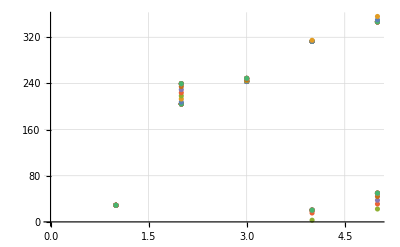

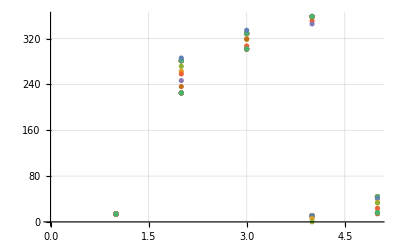

```mathematica
(*phaseShift0220=Transpose[comboEndTwiss,{1,3,2}][[1,6]]-comboStartTwiss[[1,6]];*)
phaseShiftY=comboEndTwiss[[;;,;;,6]]-comboStartTwiss[[1,6]];
phaseShiftX=comboEndTwiss[[;;,;;,3]]-comboStartTwiss[[1,3]];
(*pointList=Transpose[{Range[Length@phaseShift0220],phaseShift0220}];*)
(*ListPlot[Drop[pointList,-3]]*)
ListPlot[
Mod[phaseShiftY*360.,360.]
,GridLines->Automatic]

ListPlot[
Mod[phaseShiftX*360.,360.]
,GridLines->Automatic]
```

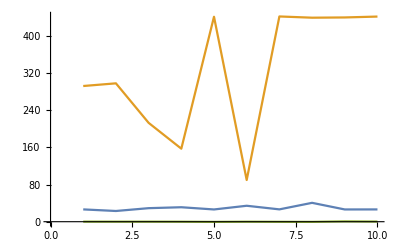

```mathematica
(*ListPlot[measurements02]*)
ListPlot[
Transpose[ws20Vars]
,AxesOrigin->{0,0}
,Joined->True
]
```

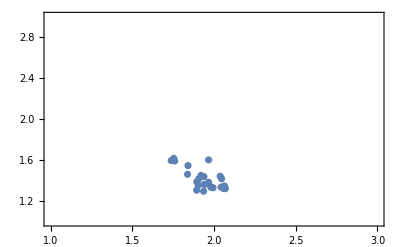

```mathematica
ListPlot[Transpose@{
moswsEndTwiss[[;;,3]]-moswsStartTwiss[[;;,3]],
moswsEndTwiss[[;;,6]]-moswsStartTwiss[[;;,6]]
}
,Frame->True
,PlotRange->{{1,3},{1,3}}
]
```

## Discussion

### Tests:

```mathematica
somwsRs[1]
```

{{{2.96397,1.2051,0,0},{-0.167998,0.269081,0,0},{0,0,101.697,799.431},{0,0,4.12377,32.4263}},{{2.37715,1.23039,0,0},{-0.178131,0.328473,0,0},{0,0,121.946,958.614},{0,0,4.12337,32.4218}},{{0.937962,1.3238,0,0},{-0.242264,0.724221,0,0},{0,0,172.976,1359.77},{0,0,4.12278,32.4151}},{{0.362501,1.52337,0,0},{-0.330298,1.37058,0,0},{0,0,196.549,1545.09},{0,0,4.12261,32.4132}}}[1]

```mathematica
somwsRs[[1]]
```

{{2.96397,1.2051,0,0},{-0.167998,0.269081,0,0},{0,0,101.697,799.431},{0,0,4.12377,32.4263}}

```mathematica
somwsRs[[1]][[1,1]]
```

2.96397

```mathematica
fullEq
```

(σ_xx[1]
σ_yy[1]
σ_xy[1]
σ_xx[2]
σ_yy[2]
σ_xy[2]
σ_xx[3]
σ_yy[3]
σ_xy[3]
σ_xx[4]
σ_yy[4]
σ_xy[4]
σ_xx[5]
σ_yy[5]
σ_xy[5]
σ_xx[6]
σ_yy[6]
σ_xy[6]
σ_xx[7]
σ_yy[7]
σ_xy[7]
σ_xx[8]
σ_yy[8]
σ_xy[8]) = (8.7851 | 7.14373 | 0 | 0 | 1.45226 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 10342.3 | 162600. | 639090.
0 | 0 | 301.427 | 2369.49 | 0 | 122.555 | 963.392 | 0 | 0 | 0
5.65084 | 5.84965 | 0 | 0 | 1.51386 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 14870.9 | 233799. | 918941.
0 | 0 | 289.884 | 2278.77 | 0 | 150.042 | 1179.47 | 0 | 0 | 0
0.879772 | 2.48334 | 0 | 0 | 1.75244 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 29920.5 | 470414. | 1.84897×10^6
0 | 0 | 162.244 | 1275.41 | 0 | 228.985 | 1800.06 | 0 | 0 | 0
0.131407 | 1.10445 | 0 | 0 | 2.32065 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 38631.7 | 607374. | 2.38731×10^6
0 | 0 | 71.2494 | 560.097 | 0 | 299.417 | 2353.74 | 0 | 0 | 0
0.131407 | 1.10445 | 0 | 0 | 2.32065 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 38631.7 | 607374. | 2.38731×10^6
0 | 0 | 71.2494 | 560.097 | 0 | 299.417 | 2353.74 | 0 | 0 | 0
0.131407 | 1.10445 | 0 | 0 | 2.32065 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 38631.7 | 607374. | 2.38731×10^6
0 | 0 | 71.2494 | 560.097 | 0 | 299.417 | 2353.74 | 0 | 0 | 0
0.0952586 | 1.08824 | 0 | 0 | 3.10804 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28455.5 | 447197. | 1.757×10^6
0 | 0 | 52.0637 | 409.108 | 0 | 297.39 | 2336.84 | 0 | 0 | 0
0.0952586 | 1.08824 | 0 | 0 | 3.10804 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 28455.5 | 447197. | 1.757×10^6
0 | 0 | 52.0637 | 409.108 | 0 | 297.39 | 2336.84 | 0 | 0 | 0).(σ[1,1]
σ[1,2]
σ[1,3]
σ[1,4]
σ[2,2]
σ[2,3]
σ[2,4]
σ[3,3]
σ[3,4]
σ[4,4])

```mathematica
r[1][1,1]
```

r[1][1,1]